```mathematica
IZOBSHTO NE E CQLOTO !!



Nesobstveni integrali
2-ri tip: pod integralnata funkciq ima vertikalna asimptota v dolnata granica na integrala, v gornata granica na integrirane ili v mejdinna to4ka

∫_a^b f(x)ⅆx = Limit t-> a+ Integral [f(x),{x,t,b}
```

integrali Nesobstveni

```mathematica
∫_0^1 1/(Sqr[e^x - 1])ⅆx
Assuming[0<t<1, ∫_0^1 1/(Sqr[e^x - 1])ⅆx]
```

∫_0^1 1/Sqr[-1+e^x]ⅆx

```mathematica
∫_0^1 1/Sqr[-1+e^x] ⅆx
Limit[%,t->0,Direction->-1]
%//N
```

∫_0^1 1/Sqr[-1+e^x]ⅆx

∫_0^1 1/Sqr[-1+e^x]ⅆx

NIntegrate::inumr: The integrand 1/Sqr[-1 + e^x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate[1/Sqr[-1+e^x],{x,0,1}]

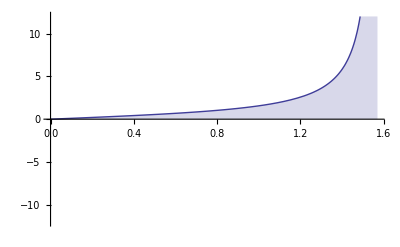

```mathematica
Plot[Tan[x],{x,0,Pi/2},Filling->Axis,PlotRange->{-12,12}]
```

```mathematica
∫_0^1 1/√(√x(1-√x))ⅆx
```

π

```mathematica
∫_0^1 1/Sqr[(1-Sqr[x]) Sqr[x]] ⅆx
Plot[1/√(√x(1-√x)),{x,0,1},PlotRange->{0,10},Filling->Axis]
```

∫_0^1 1/Sqr[(1-Sqr[x]) Sqr[x]]ⅆx

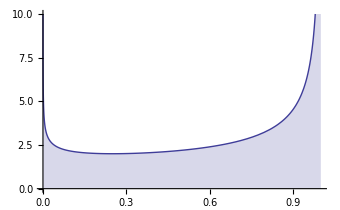
```mathematica
-Graphics-
∫1/√(√x(1-√x))ⅆx
Limit[%,x->1,Direction->1]  - Limit[%,x->0,Direction->-1]
```

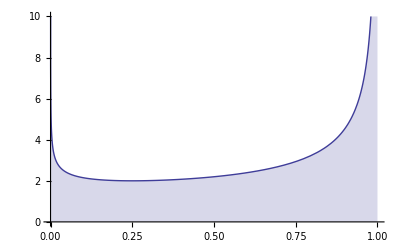

-2 √(√x-x)-ArcSin[1-2 √x]

π

```mathematica
Domashno:
Za vseki ot nesobstvenite integrali:
Namerete stoinostta mu ili opredelete,4e e razhodqsht ,kato izpolzvate nujnata definiciq za granica. Na4ertaite podintervalnata funkciq i zashtrihovaite vuprosniq raion
∫_0^2 1/(4-x^2)ⅆx
∫_0^2 1/(x^3  + 3x^2)ⅆx
∫_0^Infinity e^-3xⅆx
∫_2^Infinity 1/(x^3 - 1)ⅆx
∫_0^Infinity x*e^(-x^2)ⅆx
∫_0^(π/4) (Sin[x] + Cos[x])/√(Cos[x] - Sin[x])ⅆx
```